## Elemento isoparamétrico de 4 Nodos:

### Ing. Jorge De La Cruz. Msc. Análsis por medio de Elementos Finitos.

Definiendo las coordenadas nodales:

```mathematica
x1=0.0; y1=0.0;
x2=4.0; y2=0.0;
x3=4.0; y3=1.0;
x4=1.0;y4=1.0;
```

Graficando el elemento:

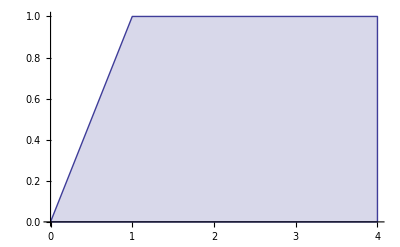

```mathematica
ListLinePlot[{{x1,y1},{x2,y2},{x3,y3},{x4,y4},{x1,y1}},Filling->Bottom]
```

Definiendo las funciones de forma en el espacio (ξ,η):

```mathematica
N1=1/4(1-ξ)(1-η);
N2=1/4(1+ξ)(1-η);
N3=1/4(1+ξ)(1+η);
N4=1/4(1-ξ)(1+η);
```

Graficando las funciones de forma:

```mathematica
Plot3D[N1,{ξ,-1,1},{η,-1,1}]
Plot3D[{N1,N2,N3,N4},{ξ,-1,1},{η,-1,1}]
```

-Graphics3D-

-Graphics3D-

Ahora podemos realizar el mapeado del sistema (ξ,η) al (x,y) utilizando la interpolación de un elemeto de 4 nodos.

```mathematica
x=Simplify[N1 x1+N2 x2+N3 x3+N4 x4]
y=Simplify[N1 y1+N2 y2+N3 y3+N4 y4]
```

2.25+η (0.25-0.25 ξ)+1.75 ξ

0.5+0.5 η

Ahora obtenemos el jacobiano de la transformación:

```mathematica
(Jmat={{D[x,ξ],D[x,η]},{D[y,ξ],D[y,η]}})//MatrixForm
```

(1.75-0.25 η | 0.25-0.25 ξ
0 | 0.5)

Ahora calculamos el determinante del Jacobiano:

```mathematica
jac=Det[Jmat]
```

0.875-0.125 η

Luego calculamos el gradiente de la función

```mathematica
(Jinv=Inverse[Jmat])//MatrixForm
```

(0.5/(0.875-0.125 η) | (-0.25+0.25 ξ)/(0.875-0.125 η)
0 | (1.75-0.25 η)/(0.875-0.125 η))

Por lo tanto ahora tenemos las derivadas inversas:

```mathematica
dξdx=Jinv[[1,1]]
dξdy=Jinv[[1,2]]
dηdx=Jinv[[2,1]]
dηdy=Jinv[[2,2]]
```

0.5/(0.875-0.125 η)

(-0.25+0.25 ξ)/(0.875-0.125 η)

0

(1.75-0.25 η)/(0.875-0.125 η)

Ahora podemos utilizar la regla de la cadena para obtener el gradiente de las funciones de forma:

```mathematica
dN1dx=D[N1,ξ]dξdx+D[N1,η]dηdx
dN1dy=D[N1,ξ]dξdy+D[N1,η]dηdy
```

(0.125 (-1+η))/(0.875-0.125 η)

((-1+η) (-0.25+0.25 ξ))/(4 (0.875-0.125 η))+((1.75-0.25 η) (-1+ξ))/(4 (0.875-0.125 η))

```mathematica
dN2dx=D[N2,ξ]dξdx+D[N2,η]dηdx
dN2dy=D[N2,ξ]dξdy+D[N2,η]dηdy
```

(0.125 (1-η))/(0.875-0.125 η)

((1.75-0.25 η) (-1-ξ))/(4 (0.875-0.125 η))+((1-η) (-0.25+0.25 ξ))/(4 (0.875-0.125 η))

```mathematica
dN3dx=D[N3,ξ]dξdx+D[N3,η]dηdx
dN3dy=D[N3,ξ]dξdy+D[N3,η]dηdy
```

(0.125 (1+η))/(0.875-0.125 η)

((1+η) (-0.25+0.25 ξ))/(4 (0.875-0.125 η))+((1.75-0.25 η) (1+ξ))/(4 (0.875-0.125 η))

```mathematica
dN4dx=D[N4,ξ]dξdx+D[N4,η]dηdx
dN4dy=D[N4,ξ]dξdy+D[N4,η]dηdy
```

(0.125 (-1-η))/(0.875-0.125 η)

((1.75-0.25 η) (1-ξ))/(4 (0.875-0.125 η))+((-1-η) (-0.25+0.25 ξ))/(4 (0.875-0.125 η))

Luego ensamblamos la matriz B:

```mathematica
(Bmat={{dN1dx,0,dN2dx,0,dN3dx,0,dN4dx,0},
{0,dN1dy,0,dN2dy,0,dN3dy,0,dN4dy},
{dN1dy,dN1dx,dN2dy,dN2dx,dN3dy,dN3dx,dN4dy,dN4dx}})//MatrixForm
```

((0.125 (-1+η))/(0.875-0.125 η) | 0 | (0.125 (1-η))/(0.875-0.125 η) | 0 | (0.125 (1+η))/(0.875-0.125 η) | 0 | (0.125 (-1-η))/(0.875-0.125 η) | 0
0 | ((-1+η) (-0.25+0.25 ξ))/(4 (0.875-0.125 η))+((1.75-0.25 η) (-1+ξ))/(4 (0.875-0.125 η)) | 0 | ((1.75-0.25 η) (-1-ξ))/(4 (0.875-0.125 η))+((1-η) (-0.25+0.25 ξ))/(4 (0.875-0.125 η)) | 0 | ((1+η) (-0.25+0.25 ξ))/(4 (0.875-0.125 η))+((1.75-0.25 η) (1+ξ))/(4 (0.875-0.125 η)) | 0 | ((1.75-0.25 η) (1-ξ))/(4 (0.875-0.125 η))+((-1-η) (-0.25+0.25 ξ))/(4 (0.875-0.125 η))
((-1+η) (-0.25+0.25 ξ))/(4 (0.875-0.125 η))+((1.75-0.25 η) (-1+ξ))/(4 (0.875-0.125 η)) | (0.125 (-1+η))/(0.875-0.125 η) | ((1.75-0.25 η) (-1-ξ))/(4 (0.875-0.125 η))+((1-η) (-0.25+0.25 ξ))/(4 (0.875-0.125 η)) | (0.125 (1-η))/(0.875-0.125 η) | ((1+η) (-0.25+0.25 ξ))/(4 (0.875-0.125 η))+((1.75-0.25 η) (1+ξ))/(4 (0.875-0.125 η)) | (0.125 (1+η))/(0.875-0.125 η) | ((1.75-0.25 η) (1-ξ))/(4 (0.875-0.125 η))+((-1-η) (-0.25+0.25 ξ))/(4 (0.875-0.125 η)) | (0.125 (-1-η))/(0.875-0.125 η))

```mathematica
ν=0.33;
Y=10.0*10^6
(Cmat=Y/(1-ν^2){{1,ν,0},{ν,1,0},{0,0,(1-ν)/2}})//MatrixForm
```

1.×10^7

(1.12221×10^7 | 3.70329×10^6 | 0.
3.70329×10^6 | 1.12221×10^7 | 0.
0. | 0. | 3.7594×10^6)

Ahora utilizamos cuadratura gaussinana para calcular la integral

```mathematica
q1=-0.5773502691;q2=-q1;w1=1.0;w2=1.0;
intg=(Transpose[Bmat].Cmat.Bmat)jac;
```

Ahora la matriz de rigidez es:

```mathematica
(ke=(intg w1 w1/.{ξ->q1,η->q1})+(intg w1 w2/.{ξ->q1,η->q2})+
(intg w2 w1/.{ξ->q2,η->q1})+(intg w2 w2/.{ξ->q2,η->q2}))//MatrixForm
```

(4.24364×10^6 | 1.53343×10^6 | 1.39546×10^6 | 318215. | -1.85126×10^6 | -1.68677×10^6 | -3.78784×10^6 | -164872.
1.53343×10^6 | 1.00196×10^7 | 346271. | 6.81357×10^6 | -1.68677×10^6 | -4.10029×10^6 | -192928. | -1.27328×10^7
1.39546×10^6 | 346271. | 6.12334×10^6 | -2.19791×10^6 | -3.78784×10^6 | -192928. | -3.73096×10^6 | 2.04457×10^6
318215. | 6.81357×10^6 | -2.19791×10^6 | 1.56306×10^7 | -164872. | -1.27328×10^7 | 2.04457×10^6 | -9.71133×10^6
-1.85126×10^6 | -1.68677×10^6 | -3.78784×10^6 | -164872. | 5.0411×10^6 | 1.48231×10^6 | 597999. | 369330.
-1.68677×10^6 | -4.10029×10^6 | -192928. | -1.27328×10^7 | 1.48231×10^6 | 1.19926×10^7 | 397385. | 4.84048×10^6
-3.78784×10^6 | -192928. | -3.73096×10^6 | 2.04457×10^6 | 597999. | 397385. | 6.9208×10^6 | -2.24903×10^6
-164872. | -1.27328×10^7 | 2.04457×10^6 | -9.71133×10^6 | 369330. | 4.84048×10^6 | -2.24903×10^6 | 1.76037×10^7)

```mathematica
(keb={ke[[1,{3,4,5,6}]],ke[[2,{3,4,5,6}]],ke[[3,{3,4,5,6}]],
ke[[4,{3,4,5,6}]],ke[[5,{3,4,5,6}]],ke[[6,{3,4,5,6}]],
ke[[7,{3,4,5,6}]],ke[[8,{3,4,5,6}]]})//MatrixForm
```

(1.39546×10^6 | 318215. | -1.85126×10^6 | -1.68677×10^6
346271. | 6.81357×10^6 | -1.68677×10^6 | -4.10029×10^6
6.12334×10^6 | -2.19791×10^6 | -3.78784×10^6 | -192928.
-2.19791×10^6 | 1.56306×10^7 | -164872. | -1.27328×10^7
-3.78784×10^6 | -164872. | 5.0411×10^6 | 1.48231×10^6
-192928. | -1.27328×10^7 | 1.48231×10^6 | 1.19926×10^7
-3.73096×10^6 | 2.04457×10^6 | 597999. | 397385.
2.04457×10^6 | -9.71133×10^6 | 369330. | 4.84048×10^6)

```mathematica
ue={0,u2,0.1,0,0.1,0,0,u8};
fe=ke.ue;
eq1=fe[[1]]==f1;eq2=fe[[2]]==0;eq3=fe[[3]]==f3;eq4=fe[[4]]==f4;eq5=fe[[5]]==f5;eq6=fe[[6]]==f6;eq7=fe[[7]]==f7;eq8=fe[[8]]==0;
Solve[eq1&&eq2&&eq3&&eq4&&eq5&&eq6&& eq7 && eq8,{f1,f3,f4,f5,f6,f7,u2,u8}]
```

{{f1→-114128.,f3→114128.,f4→-92563.2,f5→191344.,f6→92563.2,f7→-191344.,u2→-0.0500709,u8→-0.0499291}}